# ЛР3. Анимация и динамическая интерактивность - 2.

## Динамическая интерактивность курсора мыши. Локатор.

```mathematica
Manipulate[{Graphics[{White,PointSize@0.01,Point[a]},PlotRange->{{0,10},{0,10}}],a},{a,Locator}]
```

### Задание 1.

Используя локатор, смоделируйте стрельбу пользователя по мишени (нажатием курсора мыши) с выводом количества очков при попадании. В центр - 10, дальше - 9 и т.д...

### Решение.

```mathematica
getColor[a_]:=If[Norm[a]<=1,Hue[1*0.1,0.8,1],If[1<Norm[a]<=2,Hue[2*0.1,0.8,1],If[2<Norm[a]<=3,Hue[3*0.1,0.8,1],If[3<Norm[a]<=4,Hue[4*0.1,0.8,1],If[4<Norm[a]<=5,Hue[5*0.1,0.8,1],If[5<Norm[a]<=6,Hue[6*0.1,0.8,1],If[6<Norm[a]<=7,Hue[7*0.1,0.8,1],If[7<Norm[a]<=8,Hue[8*0.1,0.8,1],If[8<Norm[a]<=9,Hue[9*0.1,0.8,1],If[9<Norm[a]<=10,Hue[10*0.1,0.8,1],If[10<Norm[a],Black]]]]]]]]]]]
getHit[a_]:=If[a[[1]]==-20 &&a[[2]]==-20,"Shoot!",If[Norm[a]<=1,"10",If[1<Norm[a]<=2,"9",If[2<Norm[a]<=3,"8",If[3<Norm[a]<=4,"7",If[4<Norm[a]<=5,"6",If[5<Norm[a]<=6,"5",If[6<Norm[a]<=7,"4",If[7<Norm[a]<=8,"3",If[8<Norm[a]<=9,"2",If[9<Norm[a]<=10,"1",If[10<Norm[a],"Miss"]]]]]]]]]]]]
```

```mathematica
Manipulate[Graphics[{{Hue[#*0.1,0.8,1],Circle[{0,0},#]}&/@Range[1,10],Point[a],Text[Style[getHit[a],getColor[a],Bold,Italic,24],{8,9}]},PlotRange->{{-10,10.1},{-10.1,10}},ImageSize->Medium],{{a,{-20,-20}},Locator}]
```

```mathematica
Manipulate[Graphics[{{Hue[#*0.1,0.8,1],Disk[{0,0},#]}&/@Range[10,1,-1],Point[a],Text[Style[getHit[a],getColor[a],Bold,Italic,24],{8,9}]},PlotRange->{{-10,10.1},{-10.1,10}},ImageSize->Medium],{{a,{-20,-20}},Locator}]
```

```mathematica
Manipulate[Graphics[{{Hue[#*0.1,0.8,1],Disk[{0,0},#],White,Circle[{0,0},#]}&/@Range[10,1,-1],Point[a],Text[Style[getHit[a],getColor[a],Bold,Italic,24],{8,9}]},PlotRange->{{-10,10.1},{-10.1,10}},ImageSize->Medium],{{a,{-20,-20}},Locator}]
```

### Задание 2.

```mathematica
DynamicModule[{pts = {{0, 0}, {1, 1}, {2, 0}, {3, 2}}}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, 0, 3}, 
    PlotRange -> 3]]]]
```

Задавая локатором набор из n точек задайте и отобразите интерполяционный полином для заданного набора точек. Количество точек задавайте с помощью функции Manipulate.

### Решение.

```mathematica
InterpolatingPolynomial[{{1,9},{2,0},{3,2},{5,0}},x]
```

9+(-9+(11/2-13/8 (-3+x)) (-2+x)) (-1+x)

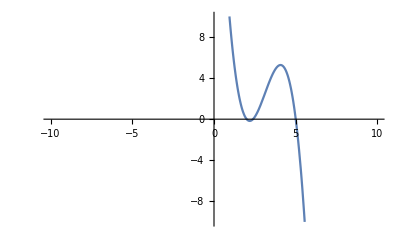

```mathematica
Plot[InterpolatingPolynomial[{{1,9},{2,0},{3,2},{5,0}},x], {x, 0,10}, 
    PlotRange -> {{-10,10},{-10,10}}]
```

```mathematica
(*Dynamic[expr] - представляет объект,который отображается как динамически обновляемое текущее значение expr. Если отображаемая форма Dynamic[expr] изменяется или редактируется в интерактивном режиме, выполняется присвоение expr=val,чтобы дать expr новое значение val,соответствующее отображаемой форме*)
Dynamic[Plot[InterpolatingPolynomial[{{1,9},{2,0},{3,2},{5,0}},x], {x, 0,10}, 
    PlotRange -> {{-10,10},{-10,10}}]]
```

```mathematica
LocatorPane[{{1,9},{2,0},{3,2},{5,0}},Dynamic[Plot[InterpolatingPolynomial[{{1,9},{2,0},{3,2},{5,0}},x], {x, 0,10}, 
    PlotRange -> {{-10,10},{-10,10}}]]]
```

```mathematica
DynamicModule[{pts = {{1,9},{2,0},{3,2},{5,0}}}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, 0, 10}, 
    PlotRange -> {{-10,10},{-10,10}}]]]]
```

```mathematica
RandomInteger[{-10,10},{5,2}]
```

{{-5,-2},{1,-8},{-6,6},{0,9},{9,10}}

```mathematica
DynamicModule[{pts = RandomReal[{-10,10},{5,2}]}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, -10, 10}, 
    PlotRange -> {{-10,10},{-10,10}}]]]]
```

```mathematica
Manipulate[DynamicModule[{pts = RandomReal[{-10,10},{a,2}]}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, -10, 10}, 
    PlotRange -> {{-10,10},{-10,10}}]]]],{a,{0,1,2,3,4,5,6,7,8,9,10}}]
```

```mathematica
Manipulate[DynamicModule[{pts = RandomReal[{-10,10},{a,2}]}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, -10, 10}, 
    PlotRange -> {{-10,10},{-10,10}}]]]],{a,{0,1,2,3,4,5,6,7,8,9,10}}]
```

## Динамическая интерактивность курсора мыши. Click Pane.

### Пример - заготовка.

```mathematica
DynamicModule[{pointlist={},a=True},Column[{Button["Refresh",pointlist={}],Button["Action",a=Not[a]],Checkbox[Dynamic@a],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Point/@pointlist,If[a,Line[pointlist]]},PlotRange->{{0,10},{0,10}},ImageSize->500],AppendTo[pointlist,#]&]}]]
```

### Задание 3.

Приведите графический интерфейс пользователя, позволяющий изобразить произвольное число точек. Координаты точек, пользователь задаёт курсором мыши. Подсветите красным две самых далёких точки множества, а зелёным две самых близких.  Выведите текстом количество точек, минимальное и максимальное расстояние на графическую область. Предусмотрите кнопку для сброса набора точек и удаления последней точки.  Ближайшие и наиболее отдалённые точки отыщите методом перебора, используя функцию DistanceMatrix.

```mathematica
pts = RandomReal[{0,10},{10,2}]
```

```mathematica
DistanceMatrix[pts]
```

### Задание 4.

Приведите графический интерфейс пользователя позволяющий изобразить треугольник и вписанную в него окружность . Координаты точек, пользователь задаёт курсором мыши .